# Solution of Optimization problem

```mathematica
(*~~~~~~~~~~~~~~~~~~~ Parameters ~~~~~~~~~~~~~~~~~~~~*) 
k=1; (*Carrying capacity: k = 1: all the abundances and the rate α are normalized to units of carrying capacity*)
maxS=1000;(*Max number of species*)
HowMany=420;(*Number of repetitions*)
where=NotebookDirectory[]<>"data-results\\Uniform-Food\\"; (*save where*)
(***************************************************)



(*~~~~~~~~~~~~~~~~~~~~~~ Loop ~~~~~~~~~~~~~~~~~~~~~~*)
Print@Dynamic@S;
Print@Dynamic@cSDev;

SetSharedVariable[data] (*for ParallellDo-loop*)

(*First Do-Loop: Parameter variation*)
Do[ 
(*First Do-Loop: Number of species*)
Do[
data={};
(*Third Do-Loop: number of repetitions. It can be parallelized or not.*)
ParallelDo[
(*************************************)
f=RandomReal[{0,1},S];(*microbial abundances in the food*)
(*f=RandomVariate[ExponentialDistribution[1],S];*)
f=f/Total[f];
r=RandomVariate[LogNormalDistribution[μ0,σ0],S];(*Growth rates*)
c=If[cSDev==0,Table[cMean,{S}],RandomVariate[TruncatedDistribution[{0,∞},NormalDistribution[cMean,cSDev]],S]];(*Clearance rates*)
(*************************************)
(*ρ: abund at fixed point;*)
(*k∞ = N/k*)
(*α∞ = α/k*)
ρ=Table[f⟦i⟧/(c⟦i⟧-r⟦i⟧+r⟦i⟧/k∞),{i,1,S}];
α∞=Sum[ρ⟦i⟧^2r⟦i⟧/f⟦i⟧Log[ρ⟦i⟧],{i,1,S}]/(Sum[ρ⟦i⟧Log[ρ⟦i⟧],{i,1,S}]Sum[ρ⟦i⟧^2r⟦i⟧/f⟦i⟧,{i,1,S}]);
(*************************************)
checkValue=0;(*if it is 0, solution converges; if it is 1, solution did not converge in the maxiteration steps*)
(*Numerical solution; when it does not converge, it changes the checkvalue to 1*)
Check[solk=FindRoot[(Total[(ρ^2 r/f)Log[ρ]]Total[ρ]-Total[ρ Log[ρ]]Total[(ρ^2 r/f)]),{k∞,0.9999/(1-Min[c/r])},MaxIterations->1000],{checkValue=1}];

sol0=k∞/.solk;(*associates the solutions of k∞ to variable sol0*)
solk=If[RealValuedNumberQ[sol0],solk,{}];(*checks if solk resulted in a good solution or not*)
(*************************************)
(*If the method resulted in a good solution, calcultes the output values; otherwise, it is gonna save an empty set*)
If[Length[solk]>0,
{
solρList=(ρ*α∞)/.solk;(*normalized microbial abundances*)
Shannon=-Total[solρList*Log[solρList]];(*Shannon diversity*)
MaxDiv=Shannon;
ShannonNorm1=Shannon/Log[S];(*Normalized shannon diversity by the max Log(S)*)
ShannonNorm2=Quiet[Shannon/Log[S-1]];(*Normalized shannon diversity by the max Log(S-1) with 1 species less*)
solk∞=k∞/.solk;(*Value of k∞*)
solα∞=α∞/.solk;(*Value of α∞*)
α=(solα∞/solk∞)*k;(*Value of α*)
nTot=α/solα∞;(*Value of N*)
solρ=solρList;
n=nTot*solρ;(*absolute microbial abundances*)
},
{
solρList={};
Shannon={};
MaxDiv={};
ShannonNorm1={};
ShannonNorm2={};
solk∞={};
solα∞={};
α={};
nTot={};
solρ={};
n={};
}
];
(*Saving the result of the repetition in the list data*)
AppendTo[data,{f,r,c,Flatten@Values[solk],solρList,Shannon,MaxDiv,ShannonNorm1,ShannonNorm2,solk∞,solα∞,α,nTot,solρ,n,checkValue}/.{ComplexInfinity->"?"}]
,{m,1,HowMany}];
(*************************************)
(*Exporting solution*)
Export[where<>"S-"<>ToString[S]<>"-species-cMean-"<>ToString[cMean]<>"-cSDev-"<>ToString[cSDev]<>"-mu-"<>ToString[μ0]<>"-sigma-"<>ToString[σ0]<>".out",data,"JSON"]
(*************************************)
(*,{S,100,maxS,10}]*)
,{S,2,99,1}]
,{cMean,{0.02}},{cSDev,{0,0.005,0.001}},{μ0,{-1.49071,-1,-2}},{σ0,{1.43846}}]
```

# Output Analysis

```mathematica
SetOptions[{Plot,ListPlot},PlotHighlighting->None]; (*Disable one dynamical visualization that is heavy for the frontend*)
```

## Importing/Exporting Files

```mathematica
(******************* Parameters ******************)
μ=-1.49071;
σ=2;
cMean=0.03;
cSDev=0.0025;

maxS=1000;
HowMany=420;
k=1;
FoodType="Uniform-Food\\";
allS=Join[Range[2,99],Range[100,maxS,10]];
fromWhere=NotebookDirectory[]<>"data-results\\"<>FoodType;
```

```mathematica
Print[Dynamic@S]
dataFile=ParallelTable[Import[fromWhere<>"S-"<>ToString[S]<>"-species-cMean-"<>ToString[cMean]<>"-cSDev-"<>ToString[cSDev]<>"-mu-"<>ToString[μ]<>"-sigma-"<>ToString[σ]<>".out","JSON"],{S,allS}];
```

### Organizing the data

```mathematica
Do[
f[allS⟦i⟧]=dataFile⟦i,All,1⟧;
r[allS⟦i⟧]=dataFile⟦i,All,2⟧;
c[allS⟦i⟧]=dataFile⟦i,All,3⟧;
solk[allS⟦i⟧]=dataFile⟦i,All,4⟧;
solρList=dataFile⟦i,All,5⟧;
Shannon[allS⟦i⟧]=dataFile⟦i,All,6⟧;
solk∞[allS⟦i⟧]=dataFile⟦i,All,10⟧;
solα∞[allS⟦i⟧]=dataFile⟦i,All,11⟧;
α[allS⟦i⟧]=dataFile⟦i,All,12⟧;
nTot[allS⟦i⟧]=dataFile⟦i,All,13⟧;
solρ[allS⟦i⟧]=dataFile⟦i,All,14⟧;
n[allS⟦i⟧]=dataFile⟦i,All,15⟧;
check[allS⟦i⟧]=dataFile⟦i,All,16⟧;
,{i,1,Length[allS]}]


Do[
NoErrorsPos[S]=Flatten@Position[check[S],x_/;x==0];

solk∞NoErrors[S]=solk∞[S]⟦#⟧&/@NoErrorsPos[S];
solα∞NoErrors[S]=solα∞[S]⟦#⟧&/@NoErrorsPos[S];
rNoErrors[S]=r[S]⟦#⟧&/@NoErrorsPos[S];
fNoErrors[S]=f[S]⟦#⟧&/@NoErrorsPos[S];
solρNoErrors[S]=solρ[S]⟦#⟧&/@NoErrorsPos[S];
ShannonNoErrors[S]=Shannon[S]⟦#⟧&/@NoErrorsPos[S];

feasiblePos[S]=Flatten@Position[solk∞NoErrors[S],x_/;x>10^-6];  
propFeasible[S]=Length[feasiblePos[S]]/(Length[NoErrorsPos[S]]);

div[S]=ShannonNoErrors[S]⟦#⟧&/@feasiblePos[S];
solk∞Feas[S]=solk∞NoErrors[S]⟦#⟧&/@feasiblePos[S];
solα∞Feas[S]=solα∞NoErrors[S]⟦#⟧&/@feasiblePos[S];
rFeas[S]=rNoErrors[S]⟦#⟧&/@feasiblePos[S];
fFeas[S]=fNoErrors[S]⟦#⟧&/@feasiblePos[S];

solρFeas[S]=solρNoErrors[S]⟦#⟧&/@feasiblePos[S];
,{S,allS}]


shannonDiv=Flatten[Table[{S,#}&/@div[S],{S,allS}],1];
```

## Images

#### Feasible Solutions

If we plot a histogram of all solutions for k/N, there is a small quantity that decrease to values close to zero.
We consider these solutions non-feasible because they are exploding solutions for the total abundance N.
Based on the histogram, we chose a cut-off value of  k/N>10^-4.

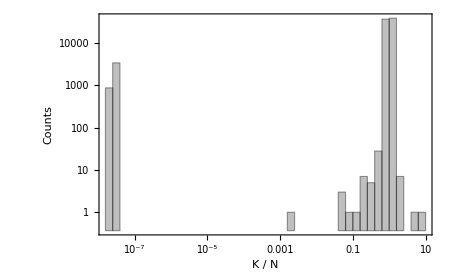

```mathematica
Histogram[
Flatten[Table[solk∞NoErrors[S],{S,allS}]],{"Log",50},
ScalingFunctions->"Log",
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
ImageSize->450,
FrameLabel->{"K / N","Counts"},
ChartStyle->Directive[EdgeForm[Black], GrayLevel[0.75]]]
```

#### Shannon Diversity X number of species

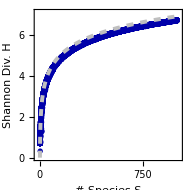

```mathematica
Show[
ShannonDivImage=ListPlot[shannonDiv,
ImageSize->190,
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
PlotStyle->{PointSize->0.02,Darker@Blue},
FrameLabel->{"# Species S","Shannon Div. H"},
PlotRange->{{-20,1020},{0,7.1}},
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
AspectRatio->1,
ImagePadding->{{40, 15}, {50,5}},
FrameTicks->{{Automatic,Automatic},{{0,250,500,750,1000},Automatic}}]
,
Plot[Log[x],{x,1,maxS},PlotStyle->Directive[Thickness[0.015],GrayLevel[0.75],Dashed],PlotRange->{{-20,1020},All}],
PlotRangePadding->None]
```

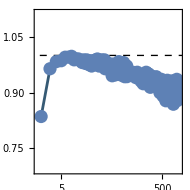

```mathematica
Show[
ListLinePlot[Table[{S,propFeasible[S]},{S,allS}],Mesh->All,ScalingFunctions->{"Log"},
Frame->True,
PlotRange->{{0,1100},{0.69,1.115}},
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
PlotStyle->{PointSize->0.05},
FrameStyle->Directive[Black,FontSize->18],
PlotStyle->{PointSize->0.02,Darker@Blue},
FrameLabel->{None,"Prop. Feasible"},
PlotRange->{{0,maxS},{0,Log[maxS]}},
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
AspectRatio->1,
FrameTicks->{{Automatic,Automatic},{{5,50,500},Automatic}},
ImageSize->190],
Plot[1,{x,0,maxS},PlotStyle->Directive[Thickness[0.005],Black,Dashed]]
]
```

Number of Errors  X  Number of Species

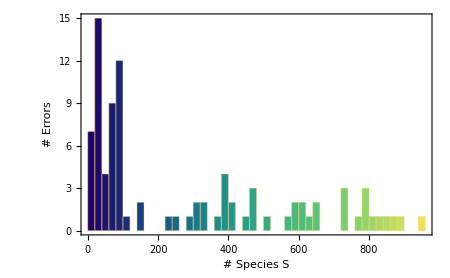

```mathematica
Histogram[
Flatten@Table[Table[S,{HowMany-Length[NoErrorsPos[S]]}],{S,allS}],50,
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
ImageSize->450,
FrameLabel->{"# Species S","# Errors"},
ChartStyle->"BlueGreenYellow"]
```

Solution α  X  N

```mathematica
rf=Mean[LogNormalDistribution[μ,σ]];
cMean0=If[cSDev==0,cMean,Mean[TruncatedDistribution[{0,∞},NormalDistribution[cMean,cSDev]]]];

alphaNImage=
Show[
Table[ListPlot[Transpose[{1/solk∞Feas[s],solα∞Feas[s]}],ImageSize->Large,PlotStyle->{PointSize->0.018,ColorData["BlueGreenYellow"][s/maxS]}],{s,allS}],
Plot[(cMean0-rf)+rf(x),{x,-0.5,3},PlotStyle->{GrayLevel[0.75],Thickness[0.015]}],
AspectRatio->1,
Frame->True,
ImageSize->190,
FrameStyle->Directive[Black,FontSize->16],
FrameLabel->{"N / K","α / N"},
AxesOrigin->{1,cMean0},AxesStyle->Directive[Gray,Thick,Dashed],
PlotRange->{{0.98,1.02},{0.005,0.035}},
FrameTicks->{{Automatic,Automatic},{{0.985,1,1.015},Automatic}},
ImagePadding->{{50, 5}, {50,5}}]
```

```mathematica
DivFoodGutImage=Show[Table[
ListPlot[Transpose@{Total/@(-fFeas[s]*Log[fFeas[s]]),div[s]},PlotStyle->{PointSize->0.02,ColorData["BlueGreenYellow"][s/maxS]},PlotRange->All]
,{s,allS}],
Plot[(x),{x,0,Log[maxS]},PlotStyle->{GrayLevel[0.75],Thickness[0.01]}],
AspectRatio->1,
Frame->True,
ImageSize->190,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{"H_F","H"},
PlotRange->{{0,7},{0,7}},
Axes->False,
PlotRangePadding->None,
ImagePadding->{{50, 5}, {45,10}}]
```

```mathematica
NkSpeciesImage=Show[
Table[
ListPlot[{S,#}&/@(1/(solk∞Feas[S])),ScalingFunctions->{"Log","Log"},PlotStyle->{PointSize->0.02,ColorData["BlueGreenYellow"][S/maxS]},FrameTicks->{{Automatic,Automatic},{{5,10,50,100,500},Automatic}}]
,{S,allS}],
Plot[1,{x,2,maxS},ScalingFunctions->{"Log","Log"},PlotStyle->{GrayLevel[0.75],Thickness[0.0075],Dashed}],
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
PlotStyle->{PointSize->0.01,Lighter@Gray},
FrameLabel->{"# Species ",""}
,PlotRange->{{1,All},All},
Axes->False,
ImageSize->190,
AspectRatio->1,
ImagePadding->{{50, 5}, {45,10}}]

alphaSpeciesImage=Show[
Table[
ListPlot[{S,#}&/@((solα∞Feas[S])/(solk∞Feas[S])),ScalingFunctions->{"Log","Log"},PlotStyle->{PointSize->0.02,ColorData["BlueGreenYellow"][S/maxS]},FrameTicks->{{Automatic,Automatic},{{5,10,50,100,500},Automatic}}]
,{S,allS}],
Plot[cMean,{x,2,maxS},ScalingFunctions->{"Log","Log"},PlotStyle->{GrayLevel[0.75],Thickness[0.0075],Dashed}],
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
PlotStyle->{PointSize->0.01,Lighter@Gray},
FrameLabel->{"# Species ",""}
,PlotRange->{{1,All},All},
Axes->False,
ImageSize->190,
AspectRatio->1,
ImagePadding->{{50, 5}, {45,10}}]
```

## Importing Data in a loop - for grids of figures

### Importing data

```mathematica
(******************* Parameters ******************)
μ=-1.49071;
σ=1.43846;
cMean=0.02;
cSDev=0.0025;

maxS=1000;
HowMany=420;
k=1;
FoodType="Uniform-Food\\";
allS=Join[Range[2,99],Range[100,maxS,10]];

paramList=
{
{μ=-1.49071,σ=1.43846,cMean=0.01,cSDev=0.0025},
{μ=-1.49071,σ=1.43846,cMean=0.015,cSDev=0.0025},
{μ=-1.49071,σ=1.43846,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=1.43846,cMean=0.025,cSDev=0.0025},
{μ=-1.49071,σ=1.43846,cMean=0.03,cSDev=0.0025},
{μ=-1.49071,σ=1.43846,cMean=0.02,cSDev=0},
{μ=-1.49071,σ=1.43846,cMean=0.02,cSDev=0.001},
{μ=-1.49071,σ=1.43846,cMean=0.02,cSDev=0.005},
{μ=-1,σ=1.43846,cMean=0.02,cSDev=0},
{μ=-1,σ=1.43846,cMean=0.02,cSDev=0.001},
{μ=-1,σ=1.43846,cMean=0.02,cSDev=0.005},
{μ=-2,σ=1.43846,cMean=0.02,cSDev=0},
{μ=-2,σ=1.43846,cMean=0.02,cSDev=0.001},
{μ=-2,σ=1.43846,cMean=0.02,cSDev=0.005},
{μ=-1.49071,σ=0.5,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=0.75,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=1.75,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=2,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=2,cMean=0.025,cSDev=0.0025},
{μ=-1.49071,σ=2,cMean=0.03,cSDev=0.0025}
};
```

```mathematica
Print[Dynamic@param];

Do[
{μ,σ,cMean,cSDev}=param;
fromWhere=NotebookDirectory[]<>"data-results\\"<>FoodType;
dataFile=ParallelTable[Import[fromWhere<>"S-"<>ToString[S]<>"-species-cMean-"<>ToString[cMean]<>"-cSDev-"<>ToString[cSDev]<>"-mu-"<>ToString[μ]<>"-sigma-"<>ToString[σ]<>".out","JSON"],{S,allS}];

sol[param]={};
err[param]={};
shannonDiv[param]={};
prop[param]={};
plotSolNα[param]={};
divFS[param]={};

Do[
(*------------Used data from the file---------*)
solk∞=dataFile⟦i,All,10⟧;
check=dataFile⟦i,All,16⟧;
f=dataFile⟦i,All,1⟧;
Shannon=dataFile⟦i,All,6⟧;
solk∞=dataFile⟦i,All,10⟧;
solα∞=dataFile⟦i,All,11⟧;

(*------------Data with no errors---------*)
NoErrorsPos=Flatten@Position[check,x_/;x==0];
solk∞NoErrors=solk∞⟦#⟧&/@NoErrorsPos;
solα∞NoErrors=solα∞⟦#⟧&/@NoErrorsPos;
fNoErrors=f⟦#⟧&/@NoErrorsPos;
ShannonNoErrors=Shannon⟦#⟧&/@NoErrorsPos;

(*------------Feasible cases---------*)
feasiblePos=Flatten@Position[solk∞NoErrors,x_/;x>10^-6];
fFeas=fNoErrors⟦#⟧&/@feasiblePos;
solk∞Feas=solk∞NoErrors⟦#⟧&/@feasiblePos;
solα∞Feas=solα∞NoErrors⟦#⟧&/@feasiblePos;
div=ShannonNoErrors⟦#⟧&/@feasiblePos;
propFeasible=Length[feasiblePos]/(Length[NoErrorsPos]);

(*------------Data to plot---------*)
AppendTo[sol[param],Evaluate[solk∞⟦#⟧&/@NoErrorsPos]];
AppendTo[err[param],Table[allS⟦i⟧,{HowMany-Length[NoErrorsPos]}]];
AppendTo[shannonDiv[param],Evaluate[{allS⟦i⟧,#}&/@div]];
AppendTo[prop[param],{allS⟦i⟧,propFeasible}];
AppendTo[plotSolNα[param],Transpose[{1/solk∞Feas,solα∞Feas}]];
AppendTo[divFS[param],Transpose[{Total/@(-fFeas*Log[fFeas]),div}]]

,{i,1,Length[allS]}];
,{param,paramList}]
```

### Final figures

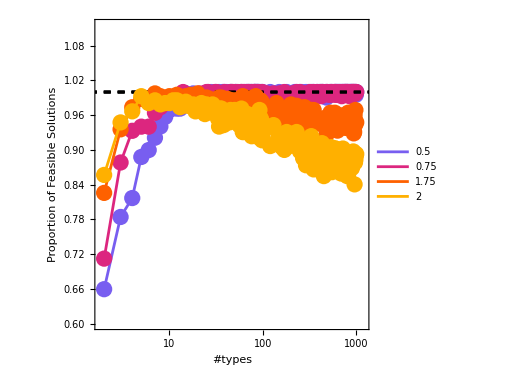

```mathematica
paramList2=
{
{μ=-1.49071,σ=0.5,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=0.75,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=1.75,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=2,cMean=0.02,cSDev=0.0025}
};

cor[1]=RGBColor["#785EF0"];
cor[2]=RGBColor["#DC267F"];
cor[3]=RGBColor["#FE6100"];
cor[4]=RGBColor["#FFB000"];

i=0;
Show@Table[
{μ,σ,cMean,cSDev}=param;
i=i+1;
Show[
ListLinePlot[prop[param],Mesh->All,ScalingFunctions->{"Log"},
Frame->True,
PlotRange->{{0,1200},{0.6,1.115}},
FrameStyle->Directive[Black,FontSize->18],
PlotStyle->{PointSize->0.03,cor[i]},
FrameLabel->{Style[Text["#types "]],"Proportion of Feasible Solutions"},
AspectRatio->1,
ImagePadding->{{75,22}, {50, 10}},
(*FrameTicks->{{Automatic,Automatic},{{2,10,50,200,1000},Automatic}},*)
ImageSize->390,
PlotLegends->LineLegend[{Automatic},{Style[Text[" "<>ToString[σ]],Black,FontSize->16]}]
],
Plot[1,{x,0,maxS},PlotStyle->Directive[Thickness[0.005],Black,Dashed]]
]
,{param,paramList2}]
```

```mathematica
paramList3=
{
{μ=-1.49071,σ=0.5,cMean=0.02,cSDev=0.0025},
{μ=-1.49071,σ=1.43846,cMean=0.02,cSDev=0.005}
};

Table[
{μ,σ,cMean,cSDev}=param;

rf=Mean[LogNormalDistribution[μ,σ]];
cMean0=If[cSDev==0,cMean,Mean[TruncatedDistribution[{0,∞},NormalDistribution[cMean,cSDev]]]];

Show[
ListPlot[plotSolNα[param],PlotStyle->Evaluate@Table[{PointSize->0.02,ColorData["BlueGreenYellow"][s/maxS]},{s,allS}],ImageSize->Large,
PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->16]],{0.82,0.16}]}
],
Plot[(cMean0-rf)+rf(x),{x,-0.5,3},PlotStyle->{GrayLevel[0.75],Thickness[0.015]}],
AspectRatio->1,
Frame->True,
ImageSize->390,
FrameStyle->Directive[Black,FontSize->18],
FrameLabel->{"",""},
AxesOrigin->{1,cMean0},AxesStyle->Directive[Gray,Thick,Dashed],
PlotRange->{{0.98,1.02},{0.005,0.035}},
(*FrameTicks->{{{{0.005,0.5},{0.015,1.5},{0.025,2.5},{0.035,3.5}},None},{{0.985,1,1.015},None}},*)
ImagePadding->{{75,22}, {50, 10}}]

,{param,paramList3}]
```

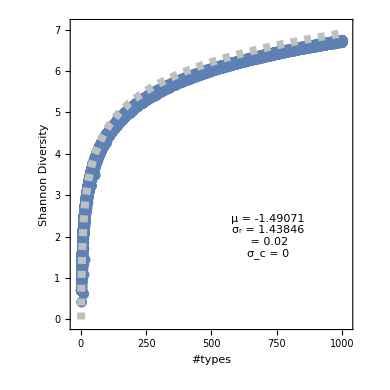

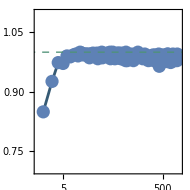

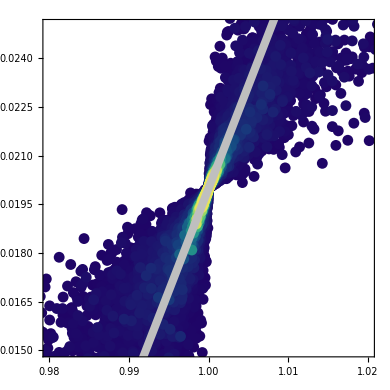

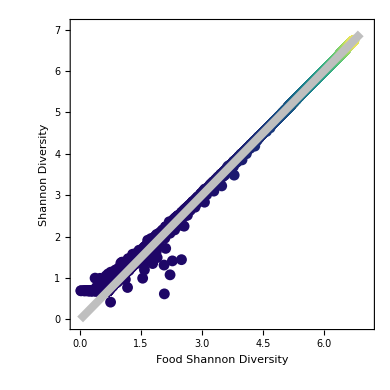

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot},
ImageSize->390,
Frame->True,
FrameStyle->Directive[Black,FontSize->18],
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
AspectRatio->1,
PlotStyle->{PointSize->0.05},
ImagePadding->{{75,22}, {50, 10}},
PlotRangePadding->None
];


Module[{param,μ=-1.49071,σ=1.43846,cMean=0.02,cSDev=0},
{
param={μ,σ,cMean,cSDev};
Print@Show[
ShannonDivImage=ListPlot[Flatten[shannonDiv[param],1],
PlotStyle->{PointSize->0.02},
FrameLabel->{Text["#types "],Text["Shannon Diversity "]},
PlotRange->{{-20,1020},{-0.1,7.1}},
(*FrameTicks->{{Automatic,Automatic},{{0,300,600,900},Automatic}},*)
PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->16]],{0.7,0.3}]}],
Plot[Log[x],{x,1,maxS},PlotStyle->Directive[Thickness[0.015],GrayLevel[0.75],Dashed],PlotRange->{{-20,1020},All},ColorFunction->None]],
(**********************)
Print@Show[
ListLinePlot[prop[param],Mesh->All,ScalingFunctions->{"Log"},
ImageSize->190,
PlotRange->{{1.5,1100},{0.7,1.1}},
FrameLabel->{Text[""],Text["Prop. Feasible"]},
FrameTicks->{{Automatic,Automatic},{{5,50,500},Automatic}},
ImagePadding->Automatic
(*PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.75,0.3}]}*)
],
Plot[1,{x,0,maxS},PlotStyle->Directive[Thickness[0.005],Black,Dashed]]
],
(**********************)
rf=Mean[LogNormalDistribution[μ,σ]],
cMean0=If[cSDev==0,cMean,Mean[TruncatedDistribution[{0,∞},NormalDistribution[cMean,cSDev]]]],
(**********************)
Print@Show[
ListPlot[plotSolNα[param],PlotStyle->Evaluate@Table[{PointSize->0.02,ColorData["BlueGreenYellow"][s/maxS]},{s,allS}],
ColorFunction->None
(*PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->16]],If[cMean<=0.02,{0.25,0.8},{0.75,0.25}]]}*)
],
Plot[(cMean0-rf)+rf(x),{x,-0.5,3},ColorFunction->None,PlotStyle->{GrayLevel[0.75],Thickness[0.015]}],
FrameLabel->{Text[""],Text[""]},
AxesOrigin->{1,cMean0},AxesStyle->Directive[Gray,Thick,Dashed],
PlotRange->{{0.98,1.02},{0.015,0.025}}
(*FrameTicks->{{{{0.005,0.5},{0.015,1.5},{0.025,2.5},{0.035,3.5}},None},{{0.985,1,1.015},None}}*)
],
(**********************)
Print@Show[
ListPlot[
divFS[param],PlotStyle->Evaluate@Table[{PointSize->0.02,ColorData["BlueGreenYellow"][s/maxS]},{s,allS}],
ColorFunction->None,
PlotRange->{{-0.1,7.1},{-0.1,7.1}}
(*PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.3,0.75}]}*)
],
Plot[(x),{x,0,Log[maxS]},ColorFunction->None,PlotStyle->{GrayLevel[0.75],Thickness[0.015]}],
FrameLabel->{Text["Food Shannon Diversity "],Text["Shannon Diversity "]},
PlotRange->{{-0.1,7.1},{-0.1,7.1}},
Axes->False
]};
]
```

### Supplementary Figures

```mathematica
solTab=Table[
{μ,σ,cMean,cSDev}=param;
Show[
Histogram[
Flatten@sol[param],
{"Log",20},
ImageSize->190,
PlotRange->{{10^-9,50},{3 10^-1,405000}},
ScalingFunctions->{None,"Log"},
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
PlotRangePadding->None,
AspectRatio->1,
FrameTicks->{{{{10,"10^1"},{1000,"10^3"},{100000,"10^5"}},None},{{{10^-6,"10^-6"},{10^-3,"10^-3"},{1,"10^0"}},None}},
ImagePadding->{{50, 5}, {50,5}},FrameLabel->{None,None},
ChartLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.55,0.75}]},
ChartStyle->Directive[GrayLevel[0.75],EdgeForm[None]]],
Plot[PDF[NormalDistribution[10^-6,10^-8],x],{x,10^-7,10^-2},PlotRange->{3 10^-1,300000},ScalingFunctions->{"Log","Log"},PlotStyle->{Red,Dashed}]
],{param,paramList}]
```

```mathematica
ErrorTab=Table[
{μ,σ,cMean,cSDev}=param;
Histogram[
{Select[Flatten@err[param],#<=100&],Select[Flatten@err[param],#>100&]},{"Log",20},"CumulativeCount",
ScalingFunctions->None,
ImageSize->190,
PlotRange->{{1,1200},{0,100}},
ChartLayout->"Stacked",
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
PlotRangePadding->0.1,
AspectRatio->1,
ImagePadding->{{50, 5}, {50,5}},
FrameLabel->{None,None},
ChartLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.3,0.75}]},
FrameTicks->{{{10,30,50,70,90},None},{{{10,"10^1"},{100,"10^2"},{1000,"10^3 "}},None}},
(*ChartStyle->Directive[EdgeForm[None]],*)
ChartStyle->{RGBColor["#648FFF"],RGBColor["#FE6100"]}
]
,{param,paramList}]
```

```mathematica
shannonTab=Table[
{μ,σ,cMean,cSDev}=param;
Show[
ShannonDivImage=ListPlot[Flatten[shannonDiv[param],1],
ImageSize->190,
Frame->True,
FrameStyle->Directive[Black,FontSize->16],
PlotStyle->{PointSize->0.02,Darker@Blue},
FrameLabel->{None,None},
PlotRange->{{-20,1020},{0.5,6.9}},
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
AspectRatio->1,
ImagePadding->{{50, 5}, {50,5}},
FrameTicks->{{Automatic,Automatic},{{0,300,600,900},Automatic}},
PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.7,0.3}]}],
Plot[Log[x],{x,1,maxS},PlotStyle->Directive[Thickness[0.015],GrayLevel[0.75],Dashed],PlotRange->{{-20,1020},All}],
PlotRangePadding->None]
,{param,paramList}]
```

```mathematica
propTab=Table[
{μ,σ,cMean,cSDev}=param;
Show[
ListLinePlot[prop[param],Mesh->All,ScalingFunctions->{"Log"},
Frame->True,
PlotRange->{{0,1100},{0.55,1.115}},
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
PlotStyle->{PointSize->0.05},
FrameStyle->Directive[Black,FontSize->16],
PlotStyle->{PointSize->0.02,Darker@Blue},
FrameLabel->{None,None},
PlotRange->{{0,maxS},{0,Log[maxS]}},
ColorFunction->Function[{x,y},ColorData["BlueGreenYellow"][x/1000]],
ColorFunctionScaling->False,
AspectRatio->1,
ImagePadding->{{50,5}, {50,5}},
FrameTicks->{{Automatic,Automatic},{{5,50,500},Automatic}},
ImageSize->{190,190},
PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.75,0.3}]}
],
Plot[1,{x,0,maxS},PlotStyle->Directive[Thickness[0.005],Black,Dashed]]
]
,{param,paramList}]
```

```mathematica
divTab=Table[
{μ,σ,cMean,cSDev}=param;
Show[
ListPlot[
divFS[param],PlotStyle->Evaluate@Table[{PointSize->0.02,ColorData["BlueGreenYellow"][s/maxS]},{s,allS}],
PlotRange->All,
PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],{0.3,0.75}]}
],
Plot[(x),{x,0,Log[maxS]},PlotStyle->{GrayLevel[0.75],Thickness[0.015]}],
AspectRatio->1,
Frame->True,
ImageSize->190,
FrameStyle->Directive[Black,FontSize->16],
FrameLabel->{None,None},
PlotRange->{{0.5,6.9},{0.5,6.9}},
Axes->False,
PlotRangePadding->None,
ImagePadding->{{50, 5}, {50,5}}
]
,{param,paramList}]
```

```mathematica
solutionTab=Table[
{μ,σ,cMean,cSDev}=param;

rf=Mean[LogNormalDistribution[μ,σ]];
cMean0=If[cSDev==0,cMean,Mean[TruncatedDistribution[{0,∞},NormalDistribution[cMean,cSDev]]]];

Show[
ListPlot[plotSolNα[param],PlotStyle->Evaluate@Table[{PointSize->0.02,ColorData["BlueGreenYellow"][s/maxS]},{s,allS}],ImageSize->Large,
PlotLegends->{Placed[Text[Style["μ = "<>ToString[μ]<>"\nσ_r = "<>ToString[σ]<>"\n = "<>ToString[cMean]<>"\nσ_c = "<>ToString[cSDev],Black,FontSize->10]],If[cMean<=0.02,{0.25,0.8},{0.75,0.25}]]}
],
Plot[(cMean0-rf)+rf(x),{x,-0.5,3},PlotStyle->{GrayLevel[0.75],Thickness[0.015]}],
AspectRatio->1,
Frame->True,
ImageSize->190,
FrameStyle->Directive[Black,FontSize->16],
FrameLabel->{None,None},
AxesOrigin->{1,cMean0},AxesStyle->Directive[Gray,Thick,Dashed],
PlotRange->{{0.98,1.02},{0.005,0.035}},
FrameTicks->{{{{0.005,0.5},{0.015,1.5},{0.025,2.5},{0.035,3.5}},None},{{0.985,1,1.015},None}},
ImagePadding->{{50, 5}, {50,5}}]

,{param,paramList}]
```

```mathematica
TITLE["prop"]="(Proportion of Feasible Solutions) X (Number of Types )";
TITLE["solution"]=" X ";
TITLE["div"]="(Gut Shannon Diversity ) X (Food Shannon Diversity )";
TITLE["shannon"]="(Maximized Shannon Diversity) X (Number of Types )";
TITLE["sol"]="Histogram of the solutions ";
TITLE["Error"]="(Cumulative number of Errors) X (Number of Types )";

paramsFiguresList={
{"prop",propTab},
{"solution",solutionTab},
{"div",divTab},
{"shannon",shannonTab},
{"sol",solTab},
{"Error",ErrorTab}
};
```

```mathematica
Do[
{NAME,IMAGE}=i;

plots1[NAME]=Grid[{
{With[{esq=27,dir=3,bai=20,cim=3},Show[IMAGE⟦1⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦2⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦3⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦4⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦5⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]}
},
Spacings->{-0.15,-0.3}];



plots1[NAME]=Grid[{
{With[{esq=27,dir=3,bai=20,cim=3},Show[IMAGE⟦1⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦2⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦3⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦4⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦5⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]}
},
Spacings->{-0.15,-0.3}];


grid1[NAME]=Grid[
{{
Labeled[Rotate[Graphics[{RGBColor[1, 0.75, 0.75],Thickness[15],Arrowheads[70],Arrow[{{0,0},{0,-2000}}]},ImageSize->{10,250}],90Degree],Style[Text[""],FontSize->22,Black],Top,Spacings->{0,-0.5}]},{
Framed[
(*Labeled[*)plots1[NAME],(*{Style[Text["# types "],FontSize->16,Black],Style[Text["Prop. of Feas. Solutions"],FontSize->16,Black]},{Bottom,Left},RotateLabel->True],*)
FrameStyle->Directive[Thickness[3],RGBColor[1, 0.75, 0.75]],RoundingRadius->5]
}},Alignment->Left
];


plots2[NAME]=Grid[{
{With[{esq=27,dir=3,bai=3,cim=3},Show[IMAGE⟦12⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=3,cim=3},Show[IMAGE⟦13⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=3,cim=3},Show[IMAGE⟦14⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]},
{With[{esq=27,dir=3,bai=3,cim=3},Show[IMAGE⟦6⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=3,cim=3},Show[IMAGE⟦7⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=3,cim=3},Show[IMAGE⟦8⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]},
{With[{esq=27,dir=3,bai=20,cim=3},Show[IMAGE⟦9⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦10⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦11⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]}
},
Spacings->{-0.15,-0.3}];


grid2[NAME]=Grid[
{{"",Labeled[Rotate[Graphics[{RGBColor[0.5, 0.75, 1],Thickness[15],Arrowheads[70],Arrow[{{0,0},{0,-2000}}]},ImageSize->{10,250}],90Degree],Style[Text[""],FontSize->22,Black],Top,Spacings->{0, -0.4}]},
{
Labeled[Graphics[{RGBColor[0.5, 0.75, 1],Thickness[15],Arrowheads[70],Arrow[{{0,0},{0,-2000}}]},ImageSize->{10,250}],Style[Text[""],FontSize->22,Black],Left],
Framed[
(*Labeled[*)plots2[NAME],(*{Style[Text["# types "],FontSize->16,Black],Style[Text["Proportion of Feasible Solutions"],FontSize->16,Black]},{Bottom,Left},RotateLabel->True],*)
FrameStyle->Directive[Thickness[3],RGBColor[0.5, 0.75, 1]],RoundingRadius->5]
}},Alignment->{Left,Top}
];

old=55;
plots3[NAME]=Grid[{
{With[{esq=27,dir=3,bai=3,cim=3},Show[IMAGE⟦15⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]},
{With[{esq=27,dir=3,bai=3,cim=3},Show[IMAGE⟦16⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]},
{With[{esq=27,dir=3,bai=3,cim=3},Show[IMAGE⟦17⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]},
{With[{esq=27,dir=3,bai=20,cim=20},Show[IMAGE⟦18⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]}
},
Spacings->{1,-0.3}];


grid3[NAME]=Grid[
{{
Labeled[Graphics[{RGBColor[0, 0.85, 0.49],Thickness[15],Arrowheads[70],Arrow[{{0,0},{0,-2000}}]},ImageSize->{10,250}],Style[Text[""],FontSize->22,Black],Left],
Framed[
(*Labeled[*)plots3[NAME],(*Style[Text["Proportion of Feasible Solutions"],FontSize->16,Black],Left,RotateLabel->True],*)
FrameStyle->Directive[Thickness[3],RGBColor[0, 0.85, 0.49]],RoundingRadius->5]
}},Alignment->Top
];


old=55;
plots4[NAME]=Grid[{
{"                         ",
With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦19⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]],With[{esq=3,dir=3,bai=20,cim=3},Show[IMAGE⟦20⟧,ImageSize->{190-old+esq+dir,190-old+bai+cim},ImagePadding->{{esq,dir},{bai,cim}}]]}
},
Spacings->{-0.15,-0.3}];


grid4[NAME]=Grid[
{{Framed[
(*Labeled[*)plots4[NAME],(*Style[Text["# types "],FontSize->16,Black],Bottom],*)
FrameStyle->Directive[Thickness[3],RGBColor[1, 0.85, 0.49]],RoundingRadius->5]
},
{
Labeled[Rotate[Graphics[{RGBColor[1, 0.85, 0.49],Thickness[15],Arrowheads[70],Arrow[{{0,0},{0,-2000}}]},ImageSize->{10,250}],90Degree],Style[Text[""],FontSize->22,Black],Bottom,Spacings->{0, 0}]}},Alignment->Left
];


over1[NAME]=Overlay[{Column[{grid3[NAME],""},Spacings->2.6],Row[{"      ",grid4[NAME]}]},Alignment->{Bottom}];
over2[NAME]=Overlay[{Column[{"",over1[NAME]},Spacings->5.5],Row[{"                                 ",grid2[NAME]}]},Alignment->Top];

GridFinal[NAME]=Evaluate@Labeled[Grid[{{"",grid1[NAME],""},{over2[NAME],SpanFromLeft}},Alignment->Left,Spacings->{1.6,1}],Style[Text[Evaluate@TITLE[NAME]],FontSize->22,Black],Top,Frame->True,FrameStyle->Directive[Thickness[3],GrayLevel[0.97]],RoundingRadius->5,FrameMargins->Small]


,{i,paramsFiguresList}]
```

```mathematica
GridFinal/@paramsFiguresList⟦All,1⟧
```

```mathematica
bar=BarLegend[{"BlueGreenYellow",{0,1000}},Ticks->{2,250,500,750,1000},LegendMarkerSize->190-55,LabelStyle->Directive[Black,FontSize->16],LegendLabel->Style[Text["# types "],Black,FontSize->16]];
leg1=LineLegend[{Directive[GrayLevel[0.75],Thickness[0.01]]},{Style[Text[""],Black,FontSize->16]},LabelStyle->Directive[Black,FontSize->16],LegendMarkerSize->30];
leg2=Evaluate@LineLegend[{Directive[GrayLevel[0.75],Thickness[0.01]]},{Style[Text[""],Black,FontSize->16]},LabelStyle->Directive[Black,FontSize->16],LegendMarkerSize->30];
leg3=LineLegend[{Directive[GrayLevel[0.75],Thickness[0.01],Dashed]},{Style[Text[""],Black,FontSize->16]},LabelStyle->Directive[Black,FontSize->16],LegendMarkerSize->30];


legenda["div"]=Grid[{{bar},{leg1}},Alignment->Left,Spacings->{0,-1}];
legenda["solution"]=Grid[{{bar},{leg2}},Alignment->Left,Spacings->{0,-1}];
legenda["shannon"]=Grid[{{bar},{leg3}},Alignment->Left,Spacings->{0,-1}];
legenda["prop"]=Grid[{{bar},{""}},Alignment->Left,Spacings->{0,-1}];

figAux1=Overlay[{GridFinal["div"],Grid[{{"",legenda["div"]},{"",""}},Spacings->{42,1.5}]},Alignment->Bottom];
figAux2=Evaluate@Overlay[{GridFinal["solution"],Evaluate@Grid[{{"",legenda["solution"]},{"",""}},Spacings->{42,1.5}]},Alignment->Bottom];
figAux3=Overlay[{GridFinal["shannon"],Grid[{{"",legenda["shannon"]},{"",""}},Spacings->{42,1.5}]},Alignment->Bottom];
figAux4=Overlay[{GridFinal["prop"],Grid[{{"",legenda["prop"]},{"",""}},Spacings->{42,3.5}]},Alignment->Bottom];
```